```mathematica
(*
Зуев В., гр. 13632/2;
Вариант 10;
*)
(*Task 1. Simplifying equation*)
clear[x];
```

```mathematica
FullSimplify[7*Sin(x)-56*(Sin^3(x))+112*(Sin^5(x))-64*(Sin^7(x))]
```

2^(1-1/2 x (1+x)) Cos x (Cos x)^x+2^(-1/2 x (1+x)) Cos (1/2 (-1-x)-x/2) x^2 (Cos x)^x Log[2]+2^(-1/2 x (1+x)) Cos x^2 (Cos x)^x (1+Log[Cos x])

-n^2 Log[n]

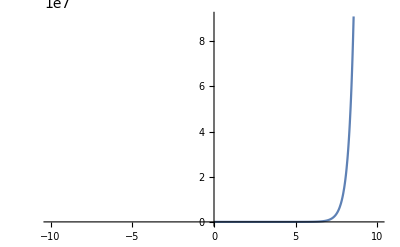

{0.692201,{x→0.367879}}

{{x1→0.529559,x2→0.421609,x3→-0.00724409}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→-1.40174-3.07964 ⅈ,x2→-0.650895-0.623067 ⅈ},{x1→-1.40174+3.07964 ⅈ,x2→-0.650895+0.623067 ⅈ},{x1→-0.196523,x2→-7.69821},{x1→3.,x2→1.5}}

{0.692201,{x→0.367879}}

{{x1→0.0806452 (6.3+0.56 x2-4.2 x3)}}

```mathematica
(*Task 2. Calculating derivative*)
D[(x*∏_(k=0)^x (Cos(x/2^k))), x]
(*Task 3. Calculating limit*)
clear[n];
Limit[(n^2-n^x)/(x-2),x->2]
(*Task 4. Defining extremal points' coordinates*)
Plot[{x^x}, {x,-10,10}]
FindMinimum[{Re[x^x], x ≥-100, x ≤100}, {x}]
clear[x]; clear[n];
(*Task 5. Solving linear equations system*)
m = {{12.4, -0.56,4.2}, {-0.65, 4.4,1.5}, {1.5,2.1 ,2.8}}
LinearSolve[m,{6.3, 1.5, 1.7}]
Solve[12.4*x1-0.56*x2+4.2x3==6.3 && -0.65x1+4.4x2+1.5x3==1.5 && 1.5x1+2.1x2-2.8x3==1.7,{x1,x2,x3}]
Clear[x1,x2,x3];
Solve[2x1*(x2)^2-4x2-7.5==0 && x1^2-3x1*x2+4.5==0,{x1,x2}]
```

```mathematica
Show[%45,ImageSize->Full]
```

-Graphics-

```mathematica
D[(Sin (7-8 Sin^2 (7-14 Sin^2+8 Sin^4)) x), x]
```

Sin (7-8 Sin^2 (7-14 Sin^2+8 Sin^4))

```mathematica
Sin (7-56 Sin^2+112 Sin^4-64 Sin^6) x
FullSimplify[Sin (7-56 Sin^2+112 Sin^4-64 Sin^6) x]
```

Sin (7-56 Sin^2+112 Sin^4-64 Sin^6) x

Sin (7-8 Sin^2 (7-14 Sin^2+8 Sin^4)) x

```mathematica
Simplify[FullSimplify Simplify (7 Sin x-56 Sin^3 x+112 Sin^5 x-64 Sin^7 x)]
```

```mathematica
FullSimplify Simplify Sin (7-56 Sin^2+112 Sin^4-64 Sin^6) x;
m = {{12.4, -0.56,4.2}, {-0.65, 4.4,1.5}, {1.5,2.1 ,2.8}};
LinearSolve[m,{6.3, 1.5, 1.7}]
```

{0.519507,0.410512,0.0209514}

```mathematica
Clear[x];
f[x_]:=x*∏_(k=0)^x (Cos[x/2^k]);
f'[x]
```

x ∂_x ∏_(k=0)^x Cos[2^-k x]+∏_(k=0)^x Cos[2^-k x]